```mathematica
Expand[(x Log[n])+(-(1/2+x)Log[j])]
```

-Log[j]/2-x Log[j]+x Log[n]

```mathematica
Expand[(-x Log[n])+(-(1/2-x)Log[j])]
```

-Log[j]/2+x Log[j]-x Log[n]

```mathematica
E^(-Log[j]/2)
```

1/(√j)

```mathematica
Expand[(-1/2-x)(j/n)^x-(-1/2+x)(j/n)^-x]
```

1/2 (j/n)^-x-1/2 (j/n)^x-(j/n)^-x x-(j/n)^x x

```mathematica
FullSimplify[j^(-1/2)(FullSimplify[3I((j/n)^3I+(j/n)^-3I)]+FullSimplify[(1/2)((j/n)^3I-(j/n)^-3I)])]/.n->10/.j->1
```

-3000003/1000-(999999 ⅈ)/2000

```mathematica
FullSimplify[(1/2)((j/n)^3I-(j/n)^-3I)]
```

(ⅈ (j^6-n^6))/(2 j^3 n^3)

```mathematica
pt[n_,x_]:=Sum[ j^(-1/2+x) n^-x (1/2+x)-j^(-1/2-x)n^x (1/2-x),{j,1,n}]
pt2[n_,x_]:=Sum[ j^(-1/2)(j^x  n^-x (1/2+x)-j^(-x)n^x (1/2-x)),{j,1,n}]
pt3[n_,x_]:=Sum[ j^(-1/2)((j/n)^x  (1/2+x)-(j/n)^(-x)(1/2-x)),{j,1,n}]
pt4[n_,x_]:=Sum[ j^(-1/2)(x((j/n)^x +(j/n)^-x  )+1/2((j/n)^x  -(j/n)^-x  )),{j,1,n}]
pt5[n_,x_]:=Sum[ j^(-1/2)(x(E^(x Log[j/n])+E^(-x Log[j/n]))+1/2(E^(x Log[j/n])-E^(-x Log[j/n]))),{j,1,n}]
pt6[n_,x_]:=Sum[ j^(-1/2)(2x Cosh[x Log[j/n]]+Sinh[x Log[j/n]]),{j,1,n}]
pt7[n_,x_]:=Sum[ j^(-1/2)(2x Cos[x Log[j/n] I]-I Sin[x Log[j/n] I]),{j,1,n}]
```

```mathematica
pt[100000,1+14.134725141734695I]
```

418355.+646413. ⅈ

```mathematica
pt6[100000,1+14.134725141734695I]
```

418355.+646413. ⅈ

```mathematica
pt7[100000,1+14.134725141734695I]
```

418355.+646413. ⅈ

```mathematica
et[x_,n_]:=Table[ (E^(x Log[j/n])+E^(-x Log[j/n])),{j,1,n}]
et2[x_,n_]:=Table[2Cosh[x Log[j/n]],{j,1,n}]
```

```mathematica
N@et[3I,8]
```

{1.99799+0. ⅈ,-1.05135+0. ⅈ,-1.96049+0. ⅈ,-0.973989+0. ⅈ,0.320187+0. ⅈ,1.30025+0. ⅈ,1.84166+0. ⅈ,2.}

```mathematica
N@et2[3I,8]
```

{1.99799,-1.05135,-1.96049,-0.973989,0.320187,1.30025,1.84166,2.}

```mathematica
pt6a[n_,x_]:=Sum[ j^(-1/2)(2x I Cos[x Log[j/n]]+I Sin[x Log[j/n]]),{j,1,n}]
pt6b[n_,x_]:=Sum[ j^(-1/2)(2x Cos[x Log[j/n]]+ Sin[x Log[j/n]]),{j,1,n}]
pt6bx[n_,x_]:={Sum[ j^(-1/2)(2x Cos[x Log[j/n]]),{j,1,n}],Sum[ j^(-1/2)(Sin[x Log[j/n]]),{j,1,n}]}
pt6by[n_,x_]:=Table[{ j^(-1/2)(2x Cos[x Log[j/n]]),j^(-1/2)(Sin[x Log[j/n]])},{j,1,n}]
pt6c[n_,x_]:=DiscretePlot[ j^(-1/2)(2x Cos[x Log[j/n]]+ Sin[x Log[j/n]]),{j,1,n}]
pt6e[n_,x_]:=DiscretePlot[ {j^(-1/2)(2x Cos[x Log[j/n]]),j^(-1/2)(Sin[x Log[j/n]])},{j,1,n}]
pt6e2[n_,x_]:=DiscretePlot[ {j^(-1/2)(2x Cos[x Log[j/n]]),j^(-1/2)(Sin[x Log[j/n]])},{j,1,n}]
pt6e2r[n_,x_]:=DiscretePlot[ {Re[j^(-1/2)(2x Cos[x Log[j/n]])],Re[j^(-1/2)(Sin[x Log[j/n]])]},{j,1,n}]
pt6e2i[n_,x_]:=DiscretePlot[ {Im[j^(-1/2)(2x Cos[x Log[j/n]])],Im[j^(-1/2)(Sin[x Log[j/n]])]},{j,1,n}]
pt6e4[n_,x_]:=DiscretePlot[ Re[{-Sum[ j^(-1/2)(2x Cos[x Log[j/n]]),{j,1,j2}],Sum[j^(-1/2)(Sin[x Log[j/n]]),{j,1,j2}]}],{j2,1,n}]
pt6e4s[n_,x_]:=DiscretePlot[ Im[{-Sum[ j^(-1/2)(2x Cos[x Log[j/n]]),{j,1,j2}],Sum[j^(-1/2)(Sin[x Log[j/n]]),{j,1,j2}]}],{j2,1,n}]
pt6e4a[n_,x_]:=DiscretePlot[ {-Sum[ j^(-1/2)(2x Cos[x Log[j/n]])/j2,{j,1,j2}],Sum[j^(-1/2)(Sin[x Log[j/n]]),{j,1,j2}]}/j2,{j2,1,n}]
pt6e5[n_,x_]:=DiscretePlot[ {-Re[Sum[ j^(-1/2)(2x Cos[x Log[j/n]]),{j,1,j2}]],Re[Sum[j^(-1/2)(Sin[x Log[j/n]]),{j,1,j2}]]},{j2,1,n}]
pt6e6[n_,x_]:=DiscretePlot[ {-Im[Sum[ j^(-1/2)(2x Cos[x Log[j/n]]),{j,1,j2}]],Im[Sum[j^(-1/2)(Sin[x Log[j/n]]),{j,1,j2}]]},{j2,1,n}]
pt6e4b[n_,x_]:=DiscretePlot[ Sum[j^(-1/2)(Sin[x Log[j/n]]),{j,1,j2}],{j2,1,n}]
pt6e4b2[n_,x_]:=DiscretePlot[ Sum[j^(-1/2)(Sin[x Log[j/n]]),{j,1,j2}],{j2,1,100}]
pt6e4b2d[n_,x_]:=DiscretePlot[j^(-1/2)(Sin[x Log[j/n]]),{j,1,100}]
pt6f[n_,x_]:=Table[j^(-1/2)(Sin[x Log[j/n]]),{j,1,50}]
```

```mathematica
pt6bx[10000,14.134725141734695  ]
```

{7.20728,-7.06593}

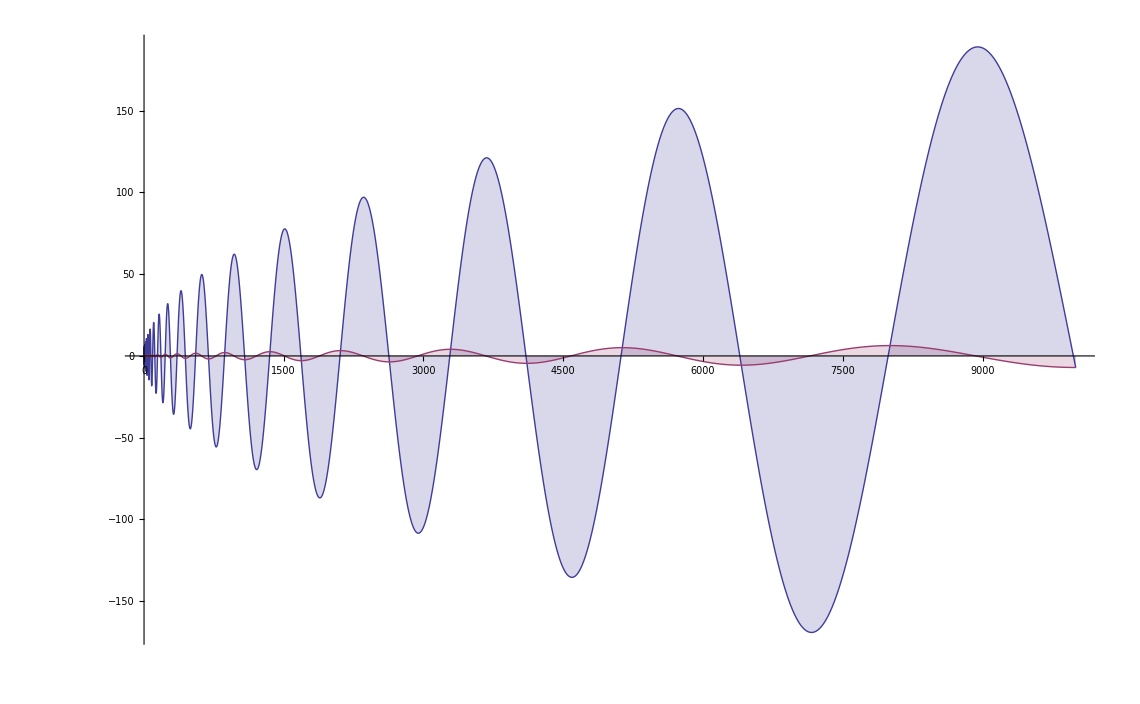

```mathematica
pt6e4[10000,14.134725141734695 ]
```

```mathematica
N@ZetaZero[10]
```

0.5+49.7738 ⅈ

```mathematica
Sin[(14.134725141734695)  Log[1.0/1000000]]
```

-0.479162

```mathematica
Animate[pt6e4b2d[x,24.134725141734695 ],{x,500,3000}]
```

```mathematica
N@pt6f[100000000,x ]//TableForm
```

-1. Sin[18.4207 x]
-0.707107 Sin[17.7275 x]
-0.57735 Sin[17.3221 x]
-0.5 Sin[17.0344 x]
-0.447214 Sin[16.8112 x]
-0.408248 Sin[16.6289 x]
-0.377964 Sin[16.4748 x]
-0.353553 Sin[16.3412 x]
-0.333333 Sin[16.2235 x]
-0.316228 Sin[16.1181 x]
-0.301511 Sin[16.0228 x]
-0.288675 Sin[15.9358 x]
-0.27735 Sin[15.8557 x]
-0.267261 Sin[15.7816 x]
-0.258199 Sin[15.7126 x]
-0.25 Sin[15.6481 x]
-0.242536 Sin[15.5875 x]
-0.235702 Sin[15.5303 x]
-0.229416 Sin[15.4762 x]
-0.223607 Sin[15.4249 x]
-0.218218 Sin[15.3762 x]
-0.213201 Sin[15.3296 x]
-0.208514 Sin[15.2852 x]
-0.204124 Sin[15.2426 x]
-0.2 Sin[15.2018 x]
-0.196116 Sin[15.1626 x]
-0.19245 Sin[15.1248 x]
-0.188982 Sin[15.0885 x]
-0.185695 Sin[15.0534 x]
-0.182574 Sin[15.0195 x]
-0.179605 Sin[14.9867 x]
-0.176777 Sin[14.9549 x]
-0.174078 Sin[14.9242 x]
-0.171499 Sin[14.8943 x]
-0.169031 Sin[14.8653 x]
-0.166667 Sin[14.8372 x]
-0.164399 Sin[14.8098 x]
-0.162221 Sin[14.7831 x]
-0.160128 Sin[14.7571 x]
-0.158114 Sin[14.7318 x]
-0.156174 Sin[14.7071 x]
-0.154303 Sin[14.683 x]
-0.152499 Sin[14.6595 x]
-0.150756 Sin[14.6365 x]
-0.149071 Sin[14.614 x]
-0.147442 Sin[14.592 x]
-0.145865 Sin[14.5705 x]
-0.144338 Sin[14.5495 x]
-0.142857 Sin[14.5289 x]
-0.141421 Sin[14.5087 x]

```mathematica
pt6b[n_,x_]:=Sum[ j^(-1/2)(2x Cos[x Log[j/n]]+ Sin[x Log[j/n]]),{j,1,n}]
pt7[n_,x_]:=(2x Sin[x Log[n]] + Cos[x Log[n]])Sum[ j^(-1/2) Sin[x Log[j]],{j,1,n}]+(2x Cos[x Log[n]] - Sin[x Log[n]])Sum[ j^(-1/2)Cos[x Log[j]],{j,1,n}]
pt7a[n_,x_]:={(2x Sin[x Log[n]] + Cos[x Log[n]])Sum[ j^(-1/2) Sin[x Log[j]],{j,1,n}],(2x Cos[x Log[n]] - Sin[x Log[n]])Sum[ j^(-1/2)Cos[x Log[j]],{j,1,n}]}
pt7b[n_,x_]:={(2x Sin[x Log[n]] + Cos[x Log[n]]),Sum[ j^(-1/2) Sin[x Log[j]],{j,1,n}],(2x Cos[x Log[n]] - Sin[x Log[n]]),Sum[ j^(-1/2)Cos[x Log[j]],{j,1,n}]}
pt7c[n_,x_]:={(2x Sin[x Log[n]] + Cos[x Log[n]]),(2x Cos[x Log[n]] - Sin[x Log[n]])}
pt7d[j_,x_]:={j^(-1/2) Sin[x Log[j]], j^(-1/2)Cos[x Log[j]]}
pt7e[n_,x_]:={Sum[j^(-1/2) Sin[x Log[j]],{j,1,n}],Sum[ j^(-1/2)Cos[x Log[j]],{j,1,n}]}
pt7ex[n_,x_]:={Sum[j^(-1/2) (-1)^(j)Sin[x Log[j]],{j,1,n}],Sum[ j^(-1/2)(-1)^(j)Cos[x Log[j]],{j,1,n}]}
pt7exa[n_,x_]:=Sum[j^(-1/2) (-1)^(j)Sin[x Log[j]],{j,1,n}]
pt7ex2[n_,x_,s_]:={Sum[j^(-1/2) (-1)^(j s)Sin[x Log[j]],{j,1,n}],Sum[ j^(-1/2)(-1)^(j s)Cos[x Log[j]],{j,1,n}]}
pt7e1[n_,x_]:=Sum[j^(-1/2) Sin[x Log[j]],{j,1,n}]
pt7e2[n_,x_]:=Sum[ j^(-1/2)Cos[x Log[j]],{j,1,n}]
pt7t1[n_,x_]:=Table[j^(-1/2) Sin[x Log[j]],{j,1,n}]
pt7t2[n_,x_]:=Table[ j^(-1/2)Cos[x Log[j]],{j,1,n}]
```

```mathematica
pt6b[1000000,14.134725141734695  ]
```

0.0141347

```mathematica
pt7[1000000,14.134725141734695  ]
```

0.0141347

```mathematica
pt7a[1000000,14.134725141734695  ]
```

{-877.254,877.268}

```mathematica
pt7b[1000000,14.134725141734695  ]
```

{14.4234,-60.8217,24.3337,36.0516}

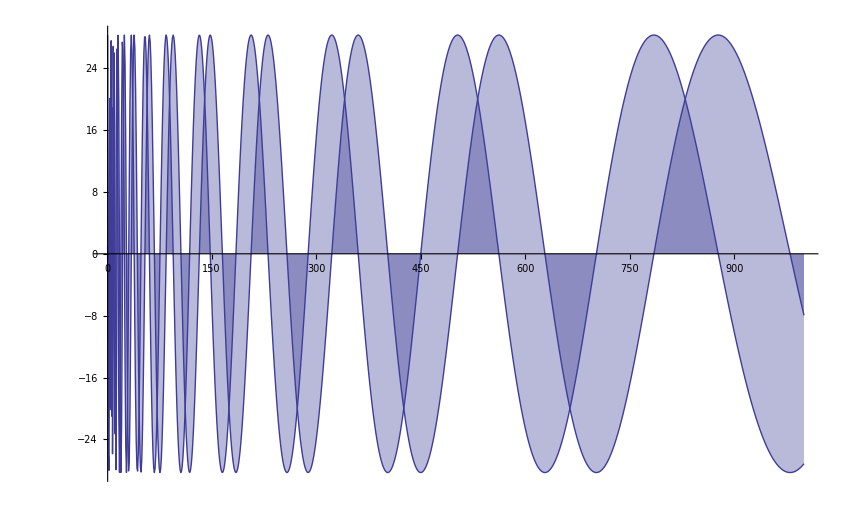

```mathematica
DiscretePlot[pt7c[n, 14.134725141734695],{n,1,1000}]
```

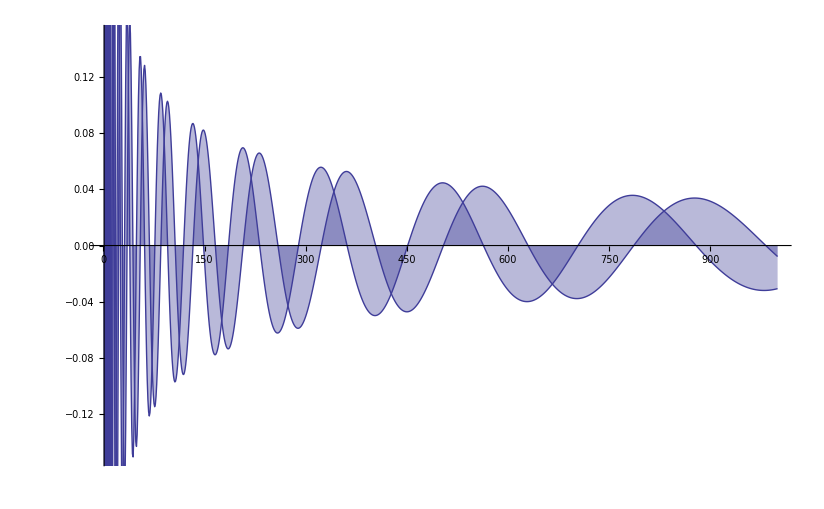

```mathematica
DiscretePlot[ pt7d[n, 14.134725141734695],{n,1,1000}]
```

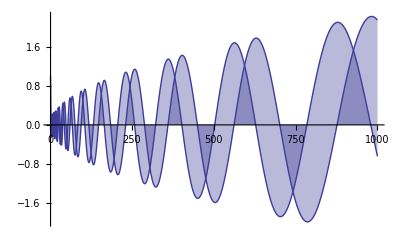

```mathematica
DiscretePlot[ pt7e[n, 14.134725141734695],{n,1,1000}]
```

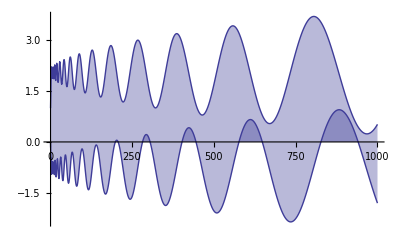

```mathematica
DiscretePlot[ pt7e[n, 3+14.134725141734695],{n,1,1000}]
```

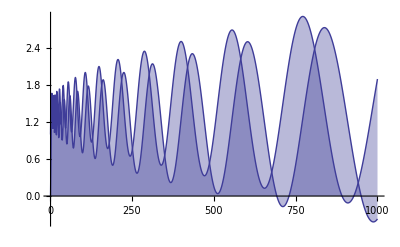

```mathematica
DiscretePlot[ pt7e[n, 5+14.134725141734695],{n,1,1000}]
```

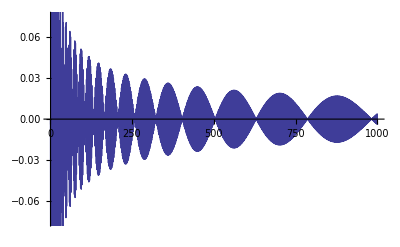

```mathematica
DiscretePlot[pt7exa[n, N@Im@ZetaZero@1],{n,1,1000}]
```

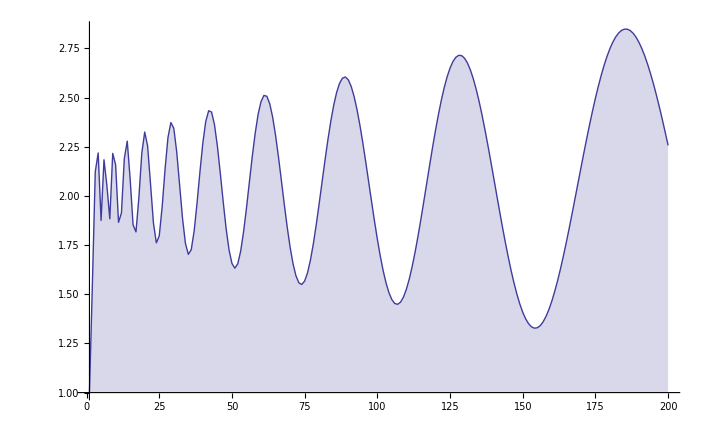

```mathematica
DiscretePlot[ pt7e2[n,3+14.134725141734695],{n,1,200}]
```

```mathematica
FullSimplify[Integrate[ 1/(j^(1/2)) Cos[ x Log[j]],{j,1,n}]]
```

ConditionalExpression[(-2+2 √n (Cos[x Log[n]]+2 x Sin[x Log[n]]))/(1+4 x^2),Re[n]≥0||n∉Reals]

```mathematica
tm[n_,x_]:= (-2+2 √n (Cos[x Log[n]]+2 x Sin[x Log[n]]))/(1+4 x^2)
```

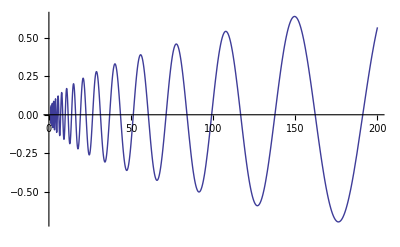

```mathematica
Plot[ tm[n,5+14.134725141734695],{n,1,200}]
```

```mathematica
FullSimplify[Integrate[ 1/(j^(1/2)) Sin[ x Log[j]],{j,1,n}]]
```

ConditionalExpression[(4 x+2 √n (-2 x Cos[x Log[n]]+Sin[x Log[n]]))/(1+4 x^2),Re[n]≥0||n∉Reals]

```mathematica
pt7f1[n_,x_]:=Sum[j^(-1/2) Sin[x Log[j]],{j,1,n}]+(4 x+2 √n (-2 x Cos[x Log[n]]+Sin[x Log[n]]))/(1+4 x^2)
pt7f2[n_,x_]:=Sum[ j^(-1/2)Cos[x Log[j]],{j,1,n}]-(-2+2 √n (Cos[x Log[n]]+2 x Sin[x Log[n]]))/(1+4 x^2)
```

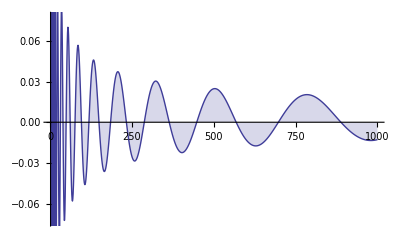

```mathematica
DiscretePlot[ pt7f2[n,14.134725141734695],{n,1,1000}]
```

```mathematica
N@pt7t2[80,x]//TableForm
```

1.
0.707107 Cos[0.693147 x]
0.57735 Cos[1.09861 x]
0.5 Cos[1.38629 x]
0.447214 Cos[1.60944 x]
0.408248 Cos[1.79176 x]
0.377964 Cos[1.94591 x]
0.353553 Cos[2.07944 x]
0.333333 Cos[2.19722 x]
0.316228 Cos[2.30259 x]
0.301511 Cos[2.3979 x]
0.288675 Cos[2.48491 x]
0.27735 Cos[2.56495 x]
0.267261 Cos[2.63906 x]
0.258199 Cos[2.70805 x]
0.25 Cos[2.77259 x]
0.242536 Cos[2.83321 x]
0.235702 Cos[2.89037 x]
0.229416 Cos[2.94444 x]
0.223607 Cos[2.99573 x]
0.218218 Cos[3.04452 x]
0.213201 Cos[3.09104 x]
0.208514 Cos[3.13549 x]
0.204124 Cos[3.17805 x]
0.2 Cos[3.21888 x]
0.196116 Cos[3.2581 x]
0.19245 Cos[3.29584 x]
0.188982 Cos[3.3322 x]
0.185695 Cos[3.3673 x]
0.182574 Cos[3.4012 x]
0.179605 Cos[3.43399 x]
0.176777 Cos[3.46574 x]
0.174078 Cos[3.49651 x]
0.171499 Cos[3.52636 x]
0.169031 Cos[3.55535 x]
0.166667 Cos[3.58352 x]
0.164399 Cos[3.61092 x]
0.162221 Cos[3.63759 x]
0.160128 Cos[3.66356 x]
0.158114 Cos[3.68888 x]
0.156174 Cos[3.71357 x]
0.154303 Cos[3.73767 x]
0.152499 Cos[3.7612 x]
0.150756 Cos[3.78419 x]
0.149071 Cos[3.80666 x]
0.147442 Cos[3.82864 x]
0.145865 Cos[3.85015 x]
0.144338 Cos[3.8712 x]
0.142857 Cos[3.89182 x]
0.141421 Cos[3.91202 x]
0.140028 Cos[3.93183 x]
0.138675 Cos[3.95124 x]
0.137361 Cos[3.97029 x]
0.136083 Cos[3.98898 x]
0.13484 Cos[4.00733 x]
0.133631 Cos[4.02535 x]
0.132453 Cos[4.04305 x]
0.131306 Cos[4.06044 x]
0.130189 Cos[4.07754 x]
0.129099 Cos[4.09434 x]
0.128037 Cos[4.11087 x]
0.127 Cos[4.12713 x]
0.125988 Cos[4.14313 x]
0.125 Cos[4.15888 x]
0.124035 Cos[4.17439 x]
0.123091 Cos[4.18965 x]
0.122169 Cos[4.20469 x]
0.121268 Cos[4.21951 x]
0.120386 Cos[4.23411 x]
0.119523 Cos[4.2485 x]
0.118678 Cos[4.26268 x]
0.117851 Cos[4.27667 x]
0.117041 Cos[4.29046 x]
0.116248 Cos[4.30407 x]
0.11547 Cos[4.31749 x]
0.114708 Cos[4.33073 x]
0.113961 Cos[4.34381 x]
0.113228 Cos[4.35671 x]
0.112509 Cos[4.36945 x]
0.111803 Cos[4.38203 x]

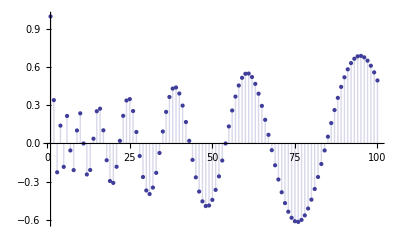

```mathematica
DiscretePlot[ pt7e2[n, 14.134725141734695],{n,1,100}]
```

```mathematica
Animate[DiscretePlot[ Re[pt7e[n, s]],{n,1,100},PlotRange->5],{s,10,260}]
```

```mathematica
pt6b[n_,x_]:=Sum[ j^(-1/2)(2x Cos[x Log[j/n]]+ Sin[x Log[j/n]]),{j,1,n}]
pt6b1[n_,x_,c_]:=Sum[ j^(-1/2)(2x Cos[x Log[j/n]+c]+ Sin[x Log[j/n]+c]),{j,1,n}]
pt6e4r[n_,x_,c_]:=DiscretePlot[ {-Sum[ j^(-1/2)(2x Cos[c+x Log[j/n]]),{j,1,j2}],Sum[j^(-1/2)(Sin[c+x Log[j/n]]),{j,1,j2}]},{j2,1,n}]
```

```mathematica
pt6b[100000,N@Im[ZetaZero[1]]]
```

0.0446979

```mathematica
pt6b1[100000,N@Im[ZetaZero[1]],0]
```

0.0446979

```mathematica
pt6b1[100000,N@Im[ZetaZero[1]],N@Pi/2]
```

632.457

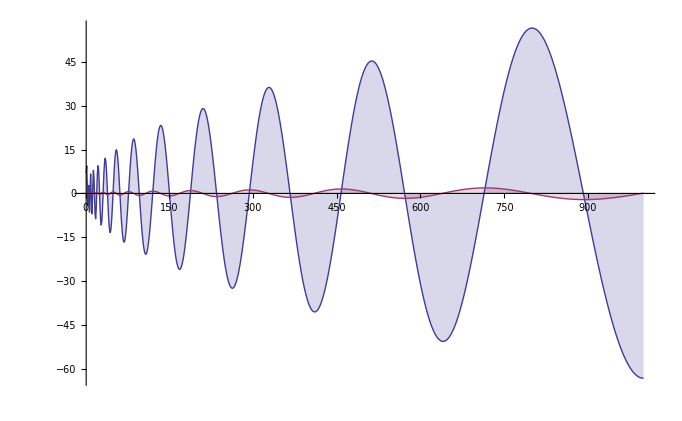

```mathematica
pt6e4r[1000,14.134725141734695 ,N@Pi/2]
```

```mathematica
pt7r[n_,x_,c_]:=(2x Sin[c+x Log[n]] + Cos[c+x Log[n]])Sum[ j^(-1/2) Sin[c+x Log[j]],{j,1,n}]+(2x Cos[c+x Log[n]] - Sin[c+x Log[n]])Sum[ j^(-1/2)Cos[c+x Log[j]],{j,1,n}]
pt7ar[n_,x_,c_]:={(2x Sin[c+x Log[n]] + Cos[c+x Log[n]])Sum[ j^(-1/2) Sin[c+x Log[j]],{j,1,n}],(2x Cos[c+x Log[n]] - Sin[c+x Log[n]])Sum[ j^(-1/2)Cos[c+x Log[j]],{j,1,n}]}
pt7cr[n_,x_,c_]:={(2x Sin[c+x Log[n]] + Cos[c+x Log[n]]),(2x Cos[c+x Log[n]] - Sin[c+x Log[n]])}
pt7dr[j_,x_,c_]:={j^(-1/2) Sin[c+x Log[j]], j^(-1/2)Cos[c+x Log[j]]}
pt7er[n_,x_,c_]:={Sum[j^(-1/2) Sin[c+x Log[j]],{j,1,n}],Sum[ j^(-1/2)Cos[c+x Log[j]],{j,1,n}]}
```

```mathematica
pt7r[10000000,14.134725141734695 ,1 ]
```

0.00446979

```mathematica
pt7r[1000000,14.134725141734695 ,2+I ]
```

0.0141347-6.86668×10^-11 ⅈ

```mathematica
pt7r[1000000,.3+14.134725141734695 ,0 ]
```

7.04051

```mathematica
pt7r[1000000,.3+14.134725141734695 ,2+I ]
```

7.04051+7.59428×10^-11 ⅈ

```mathematica
pt7r2[1000000,.3+14.134725141734695 ,1,1 ]
```

7.04051

```mathematica
pt7s[1000000,14.134725141734695 ,0]
```

-70.6593

```mathematica
Animate[DiscretePlot[ pt7ar[n, N@Im@ZetaZero[100],x],{n,1,200}],{x,0,6.28}]
```

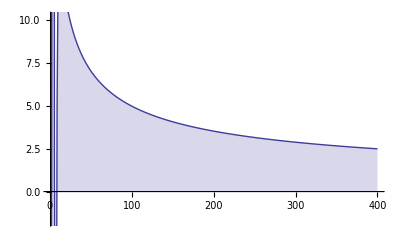

```mathematica
DiscretePlot[ pt7r[n, N@Im@ZetaZero@10,1],{n,1,400}]
```

```mathematica
D[(1-x^(1-s))Zeta[s],x]
```

-(1-s) x^-s Zeta[s]

```mathematica
FullSimplify[Gamma[1-s]/Gamma[-s-1]]
```

s (1+s)

```mathematica
D[Sum[ j^-s - (j+x n)^-s,{j,1,Infinity}],x]
```

n s HurwitzZeta[1+s,1+n x]

```mathematica
FullSimplify[Gamma[1-s]/Gamma[1-s-k]]
```

Gamma[1-s]/Gamma[1-k-s]

```mathematica
3!
```

6

```mathematica
D[n^z(s-1+z)(Zeta[s+z]-Sum[j^(-(s+z)),{j,1,n}]),z]
```

```mathematica
D[n^z(s-1+z)Zeta[s+z],z]
```

n^z Zeta[s+z]+n^z (-1+s+z) Log[n] Zeta[s+z]+n^z (-1+s+z) Zeta'[s+z]

```mathematica
D[n^z(s-1+z)(-j^(-(s+z))),z]
```

-j^(-s-z) n^z+j^(-s-z) n^z (-1+s+z) Log[j]-j^(-s-z) n^z (-1+s+z) Log[n]

```mathematica
FullSimplify[n^z ((1+(-1+s+z) Log[n]) Zeta[s+z]+(-1+s+z) Zeta'[s+z])+Sum[j^(-s-z) n^z (-1+(-1+s+z) Log[j]-(-1+s+z) Log[n]),{j,1,Infinity}]]
```

0

```mathematica
n^z ((1+(-1+s+z) Log[n]) Zeta[s+z]+(-1+s+z) Zeta'[s+z])+Sum[j^(-s-z) n^z (-1+(-1+s+z) Log[j]-(-1+s+z) Log[n]),{j,1,Infinity}]
```

-n^z (Zeta[s+z]-Log[n] Zeta[s+z]+s Log[n] Zeta[s+z]+z Log[n] Zeta[s+z]-Zeta'[s+z]+s Zeta'[s+z]+z Zeta'[s+z])+n^z ((1+(-1+s+z) Log[n]) Zeta[s+z]+(-1+s+z) Zeta'[s+z])

```mathematica
D[n^z(s-1+z)(Zeta[s+z]-Sum[j^(-(s+z)),{j,1,n}]),z]
```

n^z (-HarmonicNumber[n,s+z]+Zeta[s+z])+n^z (-1+s+z) Log[n] (-HarmonicNumber[n,s+z]+Zeta[s+z])+n^z (-1+s+z) (Zeta'[s+z]-HarmonicNumber^(0,1)[n,s+z])

```mathematica
FullSimplify[n^z Zeta[s+z]+n^z (-1+s+z) Log[n] Zeta[s+z]+n^z (-1+s+z) Zeta'[s+z] + Sum[ -j^(-s-z) n^z+j^(-s-z) n^z (-1+s+z) Log[j]-j^(-s-z) n^z (-1+s+z) Log[n],{j,1,Infinity}]]
```

0

```mathematica
D[n^z(s-1+z)(fn[a]-fx[b]),z]
```

n^z (fn[a]-fx[b])+n^z (-1+s+z) (fn[a]-fx[b]) Log[n]

```mathematica
D[fr[c](Zeta[s+z]-Sum[j^(-(s+z)),{j,1,n}]),z]
```

fr[c] (Zeta'[s+z]-HarmonicNumber^(0,1)[n,s+z])

```mathematica
Expand[x^(1-s)/(1-x^(1-s))j^-s]
```

(j^-s x^(1-s))/(1-x^(1-s))

```mathematica
Expand[(j^-s - (j+n x)^-s)/(1-x^(1-s))]
```

j^-s/(1-x^(1-s))-(j+n x)^-s/(1-x^(1-s))

```mathematica
Expand[x^(1-s)/(1-x^(1-s))(j^-s-(j+n)^-s)]
```

(j^-s x^(1-s))/(1-x^(1-s))-((j+n)^-s x^(1-s))/(1-x^(1-s))

```mathematica
Expand[((j^-s - (j+n x)^-s)/(1-x^(1-s)))-(x^(1-s)/(1-x^(1-s))(j^-s-(j+n)^-s))]
```

j^-s/(1-x^(1-s))-(j^-s x^(1-s))/(1-x^(1-s))+((j+n)^-s x^(1-s))/(1-x^(1-s))-(j+n x)^-s/(1-x^(1-s))

```mathematica
FullSimplify[((j^-s - (j+n x)^-s)/(1-x^(1-s)))-(x^(1-s)/(1-x^(1-s))(j^-s-(j+n)^-s))]
```

(-(j+n)^-s x+x^s (j+n x)^-s+j^-s (x-x^s))/(x-x^s)

```mathematica
Limit[(-(j+n)^-s x+x^s (j+n x)^-s+j^-s (x-x^s))/(x-x^s),x->1]
```

-(-(j+n)^-s-j^-s (-1+s)+j (j+n)^(-1-s) s)/(-1+s)

```mathematica
Limit[-(-(j+n)^-s-j^-s (-1+s)+j (j+n)^(-1-s) s)/(-1+s),n->Infinity]
```

Limit[-(-(j+n)^-s-j^-s (-1+s)+j (j+n)^(-1-s) s)/(-1+s),n→∞]

```mathematica
Expand[-(-(j+n)^-s-j^-s (-1+s)+j (j+n)^(-1-s) s)/(-1+s)]
```

```mathematica
ra[n_,s_]:=Sum[{-j^-s/(-1+s),+(j+n)^-s/(-1+s),+(j^-s s)/(-1+s),-(j (j+n)^(-1-s) s)/(-1+s)},{j,1,n}]
ra2[n_,s_]:=Sum[-(-(j+n)^-s-j^-s (-1+s)+j (j+n)^(-1-s) s)/(-1+s),{j,1,n}]
```

```mathematica
N@ra[2000000,.5]
```

{5653.93,-2343.15,-2826.97,343.146}

```mathematica
N@ra2[2000000,.5]
```

826.967

```mathematica
fa1[n_,s_,x_]:=Sum[ j^-s-(j+n x)^-s,{j,1,Infinity}]/(1-x^(1-s))- (x^(1-s))/(1-x^(1-s))Sum[ j^-s,{j,1,n}]
fa2[n_,s_,x_]:=Sum[ (j^-s-(j+n x)^-s)/(1-x^(1-s)),{j,1,Infinity}]- Sum[ (j^-s-(j+n)^-s)(x^(1-s))/(1-x^(1-s)),{j,1,Infinity}]
fa3[n_,s_,x_]:=Sum[ (x^s (j^-s-(j+n x)^-s))/(-x+x^s),{j,1,Infinity}]- Sum[ -((j^-s-(j+n)^-s) x)/(x-x^s),{j,1,Infinity}]
fa4[n_,s_,x_]:=Sum[-(-(j+n)^-s-j^-s (-1+s)+j (j+n)^(-1-s) s)/(-1+s),{j,1,Infinity}]
fa5[n_,s_]:=Sum[((j+n)^-s+j^-s (-1+s)-j (j+n)^(-1-s) s)/(s-1),{j,1,Infinity}]
fa6[n_,s_,t_]:=Sum[j^-s+((j+n)^-s-j (j+n)^(-1-s) s)/(s-1),{j,1,t}]
fa7[n_,s_,t_]:=Sum[j^-s+(j+n)^-s/(s-1)-(j (j+n)^(-1-s) s)/(s-1),{j,1,t}]
fa8[n_,s_,t_]:=Sum[j^-s-(j+n)^-s+(1-(1-s)^-1)(j+n)^-s-(j (j+n)^(-1-s) s)/(s-1),{j,1,t}]
fa9[n_,s_]:=Sum[j^-s,{j,1,n}]+Sum[(1-(1-s)^-1)(j+n)^-s-(j (j+n)^(-1-s) s)/(s-1),{j,1,Infinity}]
```

```mathematica
N@fa2[10000,.5+I,2]
```

$Aborted

```mathematica
Zeta[.6]
```

-1.95266

```mathematica
FullSimplify[(j^-s-(j+n x)^-s)/(1-x^(1-s))-(j^-s-(j+n)^-s)(x^(1-s))/(1-x^(1-s))]
```

(-(j+n)^-s x+x^s (j+n x)^-s+j^-s (x-x^s))/(x-x^s)

```mathematica
FullSimplify[(j^-s-(j+n x)^-s)/(1-x^(1-s))]
```

(x^s (j^-s-(j+n x)^-s))/(-x+x^s)

```mathematica
FullSimplify[(j^-s-(j+n)^-s)(x^(1-s))/(1-x^(1-s))]
```

-((j^-s-(j+n)^-s) x)/(x-x^s)

```mathematica
FullSimplify[(x^s (j^-s-(j+n x)^-s))/(-x+x^s)-(-((j^-s-(j+n)^-s) x)/(x-x^s))]
```

(-(j+n)^-s x+x^s (j+n x)^-s+j^-s (x-x^s))/(x-x^s)

```mathematica
Limit[(-(j+n)^-s x+x^s (j+n x)^-s+j^-s (x-x^s))/(x-x^s),x->1]
```

-(-(j+n)^-s-j^-s (-1+s)+j (j+n)^(-1-s) s)/(-1+s)

```mathematica
FullSimplify[-(-(j+n)^-s-j^-s (-1+s)+j (j+n)^(-1-s) s)/(-1+s)]
```

j^-s+((j+n)^(-1-s) (j+n-j s))/(-1+s)

```mathematica
FullSimplify[j^-s+((j+n)^(-1-s) (j+n-j s))/(-1+s)]
```

j^-s+((j+n)^(-1-s) (j+n-j s))/(-1+s)

```mathematica
D[ Sum[ j^-s,{j,1,n}]-(s/(1-s)Zeta[s]-Sum[s/(1-s)1/(j^(s+1)),{j,1,n}]),s]
```

HarmonicNumber[n,1+s]/(1-s)+(s HarmonicNumber[n,1+s])/(1-s)^2-Zeta[s]/(1-s)-(s Zeta[s])/(1-s)^2-(s Zeta'[s])/(1-s)+HarmonicNumber^(0,1)[n,s]+(s HarmonicNumber^(0,1)[n,1+s])/(1-s)

```mathematica
FullSimplify[-(-(j+n)^-s-j^-s (-1+s)+j (j+n)^(-1-s) s)]
```

(j+n)^-s+j^-s (-1+s)-j (j+n)^(-1-s) s

```mathematica
FullSimplify[((j+n)^-s+j^-s (-1+s)-j (j+n)^(-1-s) s)/(s-1)]
```

j^-s+((j+n)^(-1-s) (j+n-j s))/(-1+s)

```mathematica
FullSimplify[(1-s)j^-s-(j+n-j s)/(j+n)^(s+1)]
```

-j^-s (-1+s)-(j+n)^(-1-s) (j+n-j s)

```mathematica
FullSimplify[((j+n)^-s-j (j+n)^(-1-s) s)/(s-1)]
```

((j+n)^(-1-s) (j+n-j s))/(-1+s)

```mathematica
(1/(s+1))(j+n-j s)/(j+n)^(s+1)
```

```mathematica
pt6b[n_,x_]:=Sum[ j^(-1/2)(2x Cos[x Log[j/n]]+ Sin[x Log[j/n]]),{j,1,n}]
```

```mathematica
Animate[DiscretePlot[ pt7ar[n, N@Im@ZetaZero[100],x],{n,1,200}],{x,0,6.28}]
```

```mathematica
FullSimplify[Limit[(-(j+n)^-s x+x^s (j+n x)^-s+j^-s (x-x^s))/(x-x^s),x->1]]
```

j^-s+((j+n)^(-1-s) (j+n-j s))/(-1+s)

```mathematica
Limit[(-(j+n)^-s x+x^s (j+n x)^-s)/(x-x^s),x->1]
```

((j+n)^(-1-s) (j+n-j s))/(-1+s)

```mathematica
Sum[ j^-s -1/(1-s)(j+n)^-s+s n/(1-s)(j+n)^(-s-1),{j,1,Infinity}]/.s->.5/.n->10000
```

598.545

```mathematica
(-HurwitzZeta[s,1+n]+n s HurwitzZeta[1+s,1+n]-Zeta[s]+s Zeta[s])/(-1+s)/.s->.5/.n->10000000
```

-18975.1

```mathematica
N[Zeta[.5]]
```

-1.46035

```mathematica
fa5[n_,s_]:=Sum[((j+n)^-s+j^-s (-1+s)-j (j+n)^(-1-s) s)/(s-1),{j,1,Infinity}]
fa5t[n_,s_,t_]:=Sum[((j+n)^-s+j^-s (-1+s)-j (j+n)^(-1-s) s)/(s-1),{j,1,t}]
fa5a[n_,s_]:=(1/(s-1))Sum[((j+n)^-s+j^-s (-1+s)-j (j+n)^(-1-s) s),{j,1,n}]
```

```mathematica
N@fa5[10000,.45]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in j near {j} = {6.3887×10^56}. NIntegrate obtained -6.07199×10^238 and 6.07199×10^238 for the integral and error estimates.

-6.07199×10^238

```mathematica
Zeta[.4+I]
```

0.0948136-0.65653 ⅈ

```mathematica
fa1[n_,s_,x_]:=Sum[ j^-s-(j+n x)^-s,{j,1,Infinity}]/(1-x^(1-s))- (x^(1-s))/(1-x^(1-s))Sum[ j^-s,{j,1,n}]
```

```mathematica
Sum[ j^-s-(j+n x)^-s,{j,1,Infinity}]/(1-x^(1-s))
```

(-HurwitzZeta[s,1+n x]+Zeta[s])/(1-x^(1-s))

```mathematica
(x^(1-s))/(1-x^(1-s))Sum[ j^-s,{j,1,n}]
```

(x^(1-s) HarmonicNumber[n,s])/(1-x^(1-s))

```mathematica
Sum[j^-s-(j+n x)^-s,{j,1,Infinity}]/(1-x^(1-s))-(x^(1-s))/(1-x^(1-s))Sum[ j^-s,{j,1,n}]
```

-(x^(1-s) HarmonicNumber[n,s])/(1-x^(1-s))+(-HurwitzZeta[s,1+n x]+Zeta[s])/(1-x^(1-s))

```mathematica
fa1[n,s,x]/.n->10000/.s->N@ZetaZero@1/.x->2
```

-0.0000537764+0.00148849 ⅈ

```mathematica
FullSimplify[-(x^(1-s) HarmonicNumber[n,s])/(1-x^(1-s))+(-HurwitzZeta[s,1+n x]+Zeta[s])/(1-x^(1-s))]
```

(x HarmonicNumber[n,s]+x^s (HurwitzZeta[s,1+n x]-Zeta[s]))/(x-x^s)

```mathematica
Limit[(x HarmonicNumber[n,s]+x^s (HurwitzZeta[s,1+n x]-Zeta[s]))/(x-x^s),x->1]
```

(-(-1+s) HurwitzZeta[s,1+n]+n s HurwitzZeta[1+s,1+n]+(-1+s) Zeta[s])/(-1+s)

```mathematica
FullSimplify[(-(-1+s) HurwitzZeta[s,1+n]+n s HurwitzZeta[1+s,1+n]+(-1+s) Zeta[s])/(-1+s)]
```

(-(-1+s) HurwitzZeta[s,1+n]+n s HurwitzZeta[1+s,1+n]+(-1+s) Zeta[s])/(-1+s)

```mathematica
(-(-1+s) HurwitzZeta[s,1+n]+n s HurwitzZeta[1+s,1+n]+(-1+s) Zeta[s])/(-1+s)
```

```mathematica
N@Im@ZetaZero@100
```

236.524

```mathematica
`
```

```mathematica
77.1448400688748
```

```mathematica
236.5242296658162
```